# GEV Idea Test

m

## Rebuild and Test of TRS GEV Pencil

```mathematica
m=12
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
g=RandomReal[{-1,1},m];
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
Δ=0.2;
M0 = ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1=ArrayFlatten[({{0, B}, {B, 0}})];
{λs,vs} =Sort[Chop[Eigensystem[{M0,M1}]]ᵀ]ᵀ;
{y1,y2}=Partition[vs⟦1⟧,m];
pMinGEV=-Sign[g.y2] Δ y1/(√(y1.B.y1));
f[p_]:= 0.5 p.A.p + g.p
ECons[p_]:=p.B.p-Δ^2 
vars=Array[x,m];
vars0=RandomReal[{-1,1},m];
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ,PrecisionGoal->10] ;
pMinFM=vars/.FMinSub;
TableForm[{{FullForm[f[p]],ECons[p]}/.p->pMinGEV,
{FullForm[f[p]],ECons[p]}/.p->pMinFM},
TableHeadings->{{"GEV","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

12

| obj | cons: p.B.p-Δ^2
GEV | -0.720326 | -1.8735×10^-16
FindMin | -0.720326 | 9.99925×10^-9

## Extend and Test of TRS GEV Pencil

```mathematica
{m,c}={12,3};
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
g=RandomReal[{-1,1},m];
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
G=RandomReal[{-1,1},{c,m}];
Δ=0.2;
M0Big = ArrayFlatten[({{-B, A, 0}, {A, -KroneckerProduct[g,g]/Δ^2, 0}, {0, 0, ConstantArray[0,{c,c}]}})];
M1Big=ArrayFlatten[({{0, B, Gᵀ}, {B, 0, 0}, {G, 0, 0}})];
{λs,vs} =Sort[Chop[Eigensystem[{M0Big,M1Big}]]ᵀ]ᵀ;
λs
```

{-3.83599,-2.0191+0.224868 ⅈ,-2.0191-0.224868 ⅈ,-1.13095-2.30659 ⅈ,-1.13095+2.30659 ⅈ,-0.418531-0.0842568 ⅈ,-0.418531+0.0842568 ⅈ,-0.323511+0.229454 ⅈ,-0.323511-0.229454 ⅈ,-0.146844+5.33786 ⅈ,-0.146844-5.33786 ⅈ,-0.08791-0.0271893 ⅈ,-0.08791+0.0271893 ⅈ,-0.0665248,-2.37648×10^-8,2.37648×10^-8,0.159302-0.0313006 ⅈ,0.159302+0.0313006 ⅈ,0.204316-0.196461 ⅈ,0.204316+0.196461 ⅈ,0.256525,0.805966,1.29504,1.72635,2.75087,ComplexInfinity,ComplexInfinity}

```mathematica
{y1,y2}=Partition[vs⟦1,1;;2m⟧,m];λ=vs⟦1,2m+1;;-1⟧;
Map[Dimensions,{y1,y2,λ}]
```

{{12},{12},{3}}

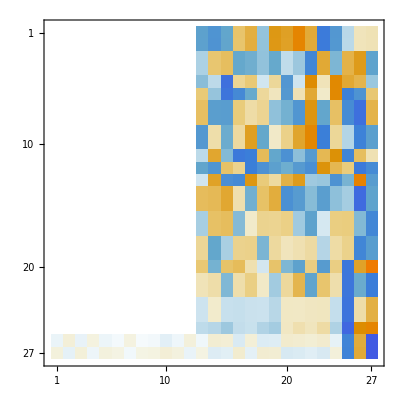

{ComplexInfinity,ComplexInfinity,-0.146844-5.33786 ⅈ,-0.146844+5.33786 ⅈ,-3.83599+0. ⅈ,2.75087+0. ⅈ,-1.13095-2.30659 ⅈ,-1.13095+2.30659 ⅈ,-2.0191+0.224868 ⅈ,-2.0191-0.224868 ⅈ,1.72635+0. ⅈ,1.29504+0. ⅈ,0.805966+0. ⅈ,-0.418531-0.0842568 ⅈ,-0.418531+0.0842568 ⅈ,-0.323511+0.229454 ⅈ,-0.323511-0.229454 ⅈ,0.204316+0.196461 ⅈ,0.204316-0.196461 ⅈ,0.256525+0. ⅈ,0.159302+0.0313006 ⅈ,0.159302-0.0313006 ⅈ,-0.08791-0.0271893 ⅈ,-0.08791+0.0271893 ⅈ,-0.0665248+0. ⅈ,2.3765×10^-8+0. ⅈ,-2.3765×10^-8+0. ⅈ}

```mathematica
MatrixPlot[NewV=Chop[Eigenvectors[{M0Big,M1Big}]]]
vv=NewV⟦-1⟧;
p1=vv⟦1;;m⟧;
Eigenvalues[{M0Big,M1Big}]
```

```mathematica
pMinGEV=-Sign[g.y2] Δ y1/(√(y1.B.y1));
f[p_]:= 0.5 p.A.p + g.p
ECons[p_]:=p.B.p-Δ^2
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
vars=Array[x,m];
vars0=RandomReal[{-1,1},m];
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ,PrecisionGoal->10] ;
pMinFM=vars/.FMinSub;
TableForm[{{FullForm[f[p]],ECons[p],G.p}/.p->pMinGEV,
{FullForm[f[p]],ECons[p]}/.p->pMinFM},
TableHeadings->{{"GEV","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

| obj | cons: p.B.p-Δ^2 | 
GEV | -0.00377929 | -6.93889×10^-18 | -0.0704259
0.0940681
0.147426
FindMin | -0.281915 | 9.99791×10^-9 |

```mathematica
?Partition
```